0.+0.98 Sin[θ[t]]+0.01 θ''[t]==0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-2. JacobiAmplitude[0.5 √(1.99+39.8 t+199. t^2),1.96985],2. JacobiAmplitude[0.5 √(1.99+39.8 t+199. t^2),1.96985]}

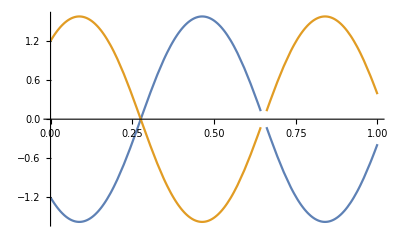

```mathematica
β=0;
g=9.8;
L=0.1;
m=0.1;
α=0;
A=0;
f=m*L*θ''[t]+β*L*θ'[t]+m*g*Sin[θ[t]]==A*Cos[α*t]
sol=DSolve[f,θ[t],t];
Evaluate[θ[t]/.sol/.{C[1]->3,C[2]->0.1}]
Plot[Evaluate[θ[t]/.sol/.{C[1]->3,C[2]->0.1}],{t,0,1}]
```